In this notebook we compare the self-consistent spectrum and pseudo-spectrum of some simple Kronecker models and the eigenvalues of the corresponding realizations.

```mathematica
SetDirectory[NotebookDirectory[]]; (*set directory*)
```

Add the folder(s) containing the Random Matrix package as well as NC package to $Path and load the packages

```mathematica
AppendTo[$Path,"/Users/yumish/Dropbox/a_recherche/mathematica_all/mathematica_packages/"];
<<NC` (*load NCAlgebra*)
<<NCAlgebra`
<<PolynomialsOfRandomMatrices`
```

* Function PlotPerturbedGinibre returns a plot of the eigenvalues and the boundary of the pseudo-spectrum, and also a list of eigenvalues (Re, Im) for a model of type G+A where G is Ginibre, and A is diagonal expectation

```mathematica
PlotPerturbedGinibre[nn_(*size of Ginibre matrix*),EExpectation_(*expectation of diagonal blocks of equal size*),rangeX_,rangeY_]:=
Block[{ginibre,aRules,aa,eV,ar,PlotEV,PlotSupport,PlotMain},
ginibre=Ginibre[nn];
aRules=Table[{i,i}->EExpectation[[1]],{i,1,nn/Length[EExpectation]}];
For[k=2,k≤Length[EExpectation],k++,
aRules=Join[aRules,Table[{i,i}->EExpectation[[k]],{i,(k-1)*nn/Length[EExpectation]+1,k*nn/Length[EExpectation]}]]
];
aa=SparseArray[aRules];
eV=Eigenvalues[ginibre+aa];
ar=(rangeY[[2]]-rangeY[[1]])/(rangeX[[2]]-rangeX[[1]]);
PlotEV=ListPlot[Table[{Re[eV[[i]]],Im[eV[[i]]]},{i,Length[eV]}],PlotRange->{rangeX,rangeY},AspectRatio->ar,PlotStyle->{GrayLevel[0.45],PointSize[0.003]}];
PlotSupport=ContourPlot[Sum[1/((x-Re[EExpectation[[i]]])^2+(y-Im[EExpectation[[i]]])^2),{i,Length[EExpectation]}]==Length[EExpectation],{x,rangeX[[1]],rangeX[[2]]},{y,rangeY[[1]],rangeY[[2]]},ContourStyle->GrayLevel[0.0],PerformanceGoal->"Quality",WorkingPrecision->100,MaxRecursion->10,Axes->True];
PlotMain=Show[PlotEV,PlotSupport,ImageSize->420,PlotRange->{rangeX,rangeY},Axes->False,Frame->True,BaseStyle->{FontSize->16,FontFamily->"Latin Modern Roman"},FrameLabel->{"Re(ζ)","Im(ζ)"}];
Return[{PlotMain,Table[{Re[eV[[i]]],Im[eV[[i]]]},{i,Length[eV]}]}];
];
```

Basic example 1: Ginibre + Diag(1,-1)

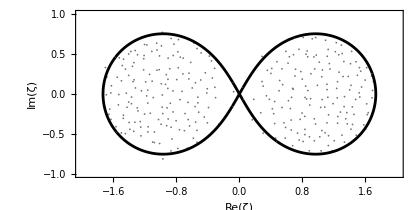

```mathematica
PlotPerturbedGinibre[300,{-1,1},{-2,2},{-1,1}][[1]]
```

Basic example 2: Ginibre +Diag(0,-1.4,1.4,-0.8+ⅈ1.26,0.8+ⅈ1.26)

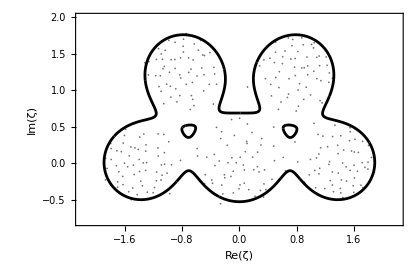

```mathematica
EExpectation={0,-1.4,1.4,-0.8+ⅈ*1.26,0.8+ⅈ*1.26};
PlotPerturbedGinibre[300,EExpectation,{-2.2,2.2},{-0.8,2}][[1]]
```

## Examples

### Eigenvalues of a Ginibre matrix with diagonal expectation + the boundary of the support of the Brown measure computed analytically

We see that the support of the bulk of the eigenvalues coincides with boundary of the support of the Brown measure obtained in the paper

Ginibre + Diag[-1, 1]

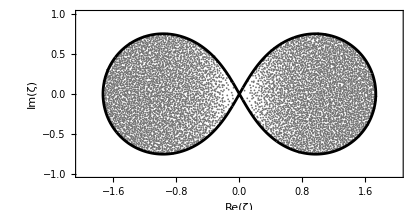

```mathematica
Result1=PlotPerturbedGinibre[8000,{-1,1},{-2,2},{-1,1}];
Result1[[1]]
```

```mathematica
Ginibre + Diag[-0.97, 0.97]
```

Ginibre+Diag[-0.97,0.97]

ContourPlot::precw: The precision of the argument function ({((0.97+x)^2+y^2)-0,((-0.97+x)^2+y^2)-0}) is less than WorkingPrecision (100.).

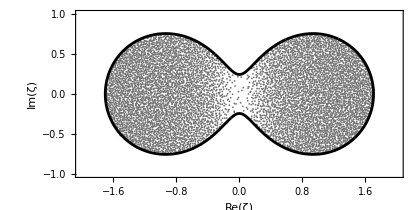

```mathematica
Result097=PlotPerturbedGinibre[8000,{-0.97,0.97},{-2,2},{-1,1}];
Result097[[1]]
```

```mathematica
Ginibre + Diag[-1.03, 1.03]
```

Ginibre+Diag[-1.03,1.03]

ContourPlot::precw: The precision of the argument function ({((1.03+x)^2+y^2)-0,((-1.03+x)^2+y^2)-0}) is less than WorkingPrecision (100.).

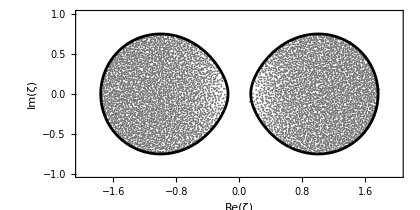

```mathematica
Result103=PlotPerturbedGinibre[8000,{-1.03,1.03},{-2,2},{-1,1}];
Result103[[1]]
```

```mathematica
Ginibre + Diag[0,-1.4,1.4,-0.8+ⅈ*1.26,0.8+ⅈ*1.26]
```

Ginibre+Diag[0,-1.4,1.4,-0.8+1.26 ⅈ,0.8+1.26 ⅈ]

ContourPlot::precw: The precision of the argument function ({((1.4+x)^2+y^2)-0,(x^2+y^2)-0,((-1.4+x)^2+y^2)-0,((0.8+x)^2+(-1.26+y)^2)-0,((-0.8+x)^2+(-1.26+y)^2)-0}) is less than WorkingPrecision (100.).

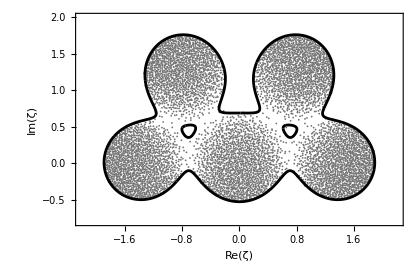

```mathematica
EExpectation={0,-1.4,1.4,-0.8+ⅈ*1.26,0.8+ⅈ*1.26};
Result5disks=PlotPerturbedGinibre[8000,EExpectation,{-2.2,2.2},{-0.8,2}];
Result5disks[[1]]
Export[NotebookDirectory[]<>"/plots/Plot5disks.pdf",Result5disks[[1]]];
Export[NotebookDirectory[]<>"/plots/EV5disks.mat",Result5disks[[2]]];
```

### Eigenvalues of a random matrix with Ginibre blocks perturbed by a Jordan block

We compute the eigenvalues, which indicate the support of the empirical spectral measure. We can show that the support of the ESM is very well predicted by the pseudo-spectrum computed using the Dyson equation (not computed in this notebook)

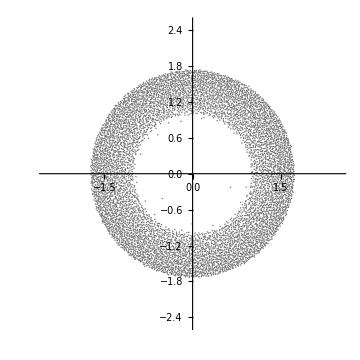

```mathematica
a=Sqrt[2];
nn=8000;
ginibre=Ginibre[nn];
aRules=Table[{i,i+1}->a,{i,1,nn-1}];
aa=SparseArray[aRules,{nn,nn}];
eV=Eigenvalues[ginibre+aa];
PlotEV=ListPlot[Table[{Re[eV[[i]]],Im[eV[[i]]]},{i,Length[eV]}],PlotRange->{{-2.5,2.5},{-2.5,2.5}},AspectRatio->1,PlotStyle->{GrayLevel[0.45],PointSize[0.0028]}, ImageSize->Medium]
```

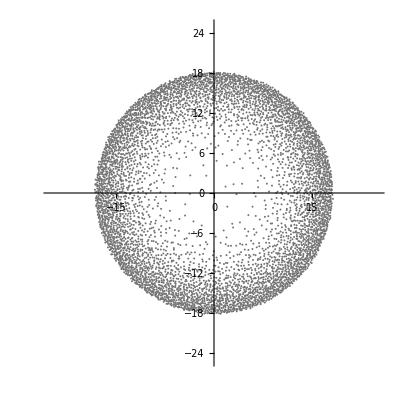

```mathematica
a=100;
r=a/4;
nn=6000;
RangeXY={{-r,r},{-r,r}};
ginibre=Ginibre[nn];
aRules=Table[{i,i+nn/3}->a,{i,1,nn/3}];
For[k=2,k≤2,k++,
aRules=Join[aRules,Table[{i,i+nn/3}->a,{i,(k-1)*nn/3+1,k*nn/3}]]
];
aa=SparseArray[aRules,{nn,nn}];
eV=Eigenvalues[ginibre+aa];
PlotEV=ListPlot[Table[{Re[eV[[i]]],Im[eV[[i]]]},{i,Length[eV]}],PlotRange->RangeXY,AspectRatio->1,PlotStyle->{GrayLevel[0.45],PointSize[0.0035]}]
```

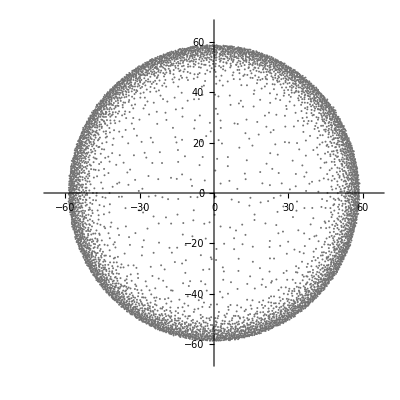

```mathematica
a=100;
r=a * 0.66;
nn=6000;
RangeXY={{-r,r},{-r,r}};
ginibre=Ginibre[nn];
aRules=Table[{i,i+nn/10}->a,{i,1,nn/10}];
For[k=2,k≤9,k++,
aRules=Join[aRules,Table[{i,i+nn/10}->a,{i,(k-1)*nn/10+1,k*nn/10}]]
];
aa=SparseArray[aRules,{nn,nn}];
eV=Eigenvalues[ginibre+aa];
PlotEV=ListPlot[Table[{Re[eV[[i]]],Im[eV[[i]]]},{i,Length[eV]}],PlotRange->RangeXY,AspectRatio->1,PlotStyle->{GrayLevel[0.45],PointSize[0.0035]}];
PlotEV
```

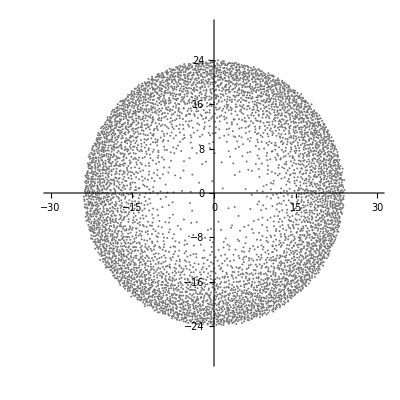

```mathematica
a=100;
r=a* 0.3;
nn=6000;
RangeXY={{-r,r},{-r,r}};
ginibre=Ginibre[nn];
ginibre[[1;;nn/3,1;;nn/3]]=20*ginibre[[1;;nn/3,1;;nn/3]];
aRules=Table[{i,i+nn/3}->a,{i,1,nn/3}];
For[k=2,k≤2,k++,
aRules=Join[aRules,Table[{i,i+nn/3}->-a*2,{i,(k-1)*nn/3+1,k*nn/3}]]
];
aa=SparseArray[aRules,{nn,nn}];
eV=Eigenvalues[ginibre+aa];
PlotEV=ListPlot[Table[{Re[eV[[i]]],Im[eV[[i]]]},{i,Length[eV]}],PlotRange->RangeXY,AspectRatio->1,PlotStyle->{GrayLevel[0.45],PointSize[0.0035]}];
PlotEV
```

Illustration of how the self-consistent density of states of the hermitized model detects the boundary of the support of Kronecker matrices

Below we change the values of the hermitization parameter ζ and compute the corresponding self-consistent density. We see that as the point ζ crosses the boundary of the support, the self-consistent density vanishes at the origin.

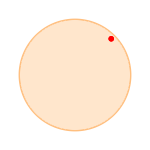
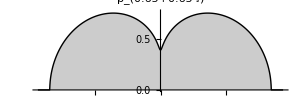
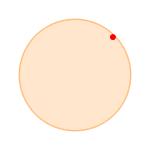
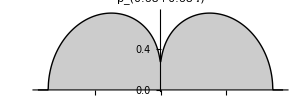
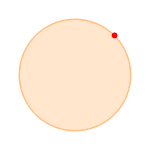
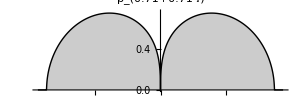
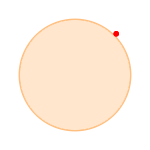
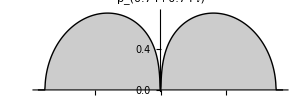
{{ζ=0.65(1 + ⅈ),-Graphics-,-Graphics-},{ζ=0.68(1 + ⅈ),-Graphics-,-Graphics-},{ζ=0.71(1 + ⅈ),-Graphics-,-Graphics-},{ζ=0.74(1 + ⅈ),-Graphics-,-Graphics-},{ζ=0.77(1 + ⅈ),-Graphics-,-Graphics-},{ζ=0.8(1 + ⅈ),-Graphics-,-Graphics-},{ζ=0.83(1 + ⅈ),-Graphics-,-Graphics-}}

```mathematica
Clear[ζ];
zList=Range[0.65, 0.84, 0.03];
Table[
ζ=zList[[k]]*(1 + ⅈ);
int=2.8;
IInterval={-int,int};
A={{0,-ζ},{-Conjugate[ζ],0}};
LL={{{0,1/Sqrt[2]},{1/Sqrt[2],0}},{{0,ⅈ/Sqrt[2]},{-ⅈ/Sqrt[2],0}}};
II=IdentityMatrix[Length[A]];
SSOperator[R_]:=Total[Table[LL[[i]].R.LL[[i]],{i,Length[LL]}]];

KK=500000; ϵϵ=0.000001;
 ηη=0.00001; LLPoints=1000;

MM=IterativelySolveMDEonInterval[SSOperator,A,II,IInterval[[1]],IInterval[[2]],ηη,LLPoints,KK,ϵϵ];

{"ζ=" <> ToString[zList[[k]]] <>"(1 + ⅈ)", Show[ContourPlot[x^2+y^2,{x,-1,1},{y,-1,1},Contours->{1},ContourStyle->Directive[Orange,Thick],ColorFunction->(If[#1>1/2,White,LightOrange]&)],ListPlot[{{zList[[k]],zList[[k]]}}, AspectRatio->1,PlotMarkers->{"o",14},PlotStyle->{Red,Thick}],PlotRange->{{-1.1,1.1},{-1.1,1.1}},FrameTicksStyle->{{FontSize->14,FontFamily->"Serif"},{FontSize->16,FontFamily->"Serif"}},ImageSize->150,Axes->False,Frame->False],ListLinePlot[
Table[{MM[[i,1]],Im[MM[[i,2]][[1,1]]]},{i,Length[MM]}],
PlotRange->{0,1.02 Max[Table[Im[MM[[i,2]][[1,1]]],{i,Length[MM]}]]},Ticks->Automatic,PlotLegends->Automatic,ImageSize->300,AspectRatio->1/3,Axes->{True,False},PlotStyle->{Black,Thick},TicksStyle->{{FontSize->12,FontFamily->"Serif"},{FontSize->12,FontFamily->"Serif"}},PlotLabel->Style[Subscript[ρ, ζ],16,FontFamily->"Serif"],Filling->Bottom]},{k,1,Length[zList]}]
```